```mathematica
p = Plot3D[x^2 + 1.5*y^3, {x,0,1}, {y,-1,1}]
```

-Graphics3D-

```mathematica
Export["/usr0/home/bbohrer/research/hilbert-epsilon/img/plot1.pdf",p,"PDF"]
```

/usr0/home/bbohrer/research/hilbert-epsilon/img/plot1.pdf

ImplicitRegion::bcond: x/y should be a Boolean combination of equations, inequalities, and Element statements.

```mathematica
q = p = Plot3D[x/y, {x,-1,1}, {y,-1,1}]
```

-Graphics3D-

```mathematica
Export["/usr0/home/bbohrer/research/hilbert-epsilon/img/plot2.pdf",q,"PDF"]
```

/usr0/home/bbohrer/research/hilbert-epsilon/img/plot2.pdf

RGBColor[0.2, 0.2, 0.2]

Set::write: Tag Slot in #r1 is Protected.

Set::write: Tag Slot in #r3 is Protected.

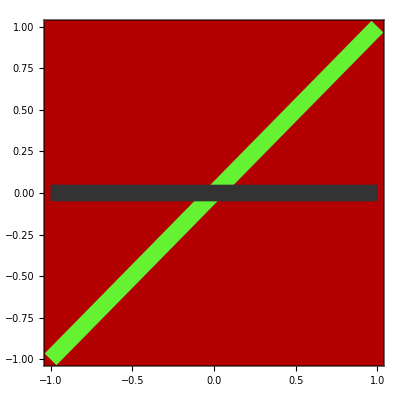

```mathematica
greencolor = RGBColor[100/255,255/255,200/255];
darkgreencolor = RGBColor[.1,.3,0];
redcolor =RGBColor[.7,0,0];
bluecolor=RGBColor[.14,.21,.868];
graycolor = RGBColor[.2,.2,.2]
trueStyle = {Directive[Opacity[1],RGBColor[Rational[20, 51], 0.9500000000000001, 0.2],Thickness[0.03]]};
falseStyle = {Directive[Opacity[1], redcolor, Thickness[0.03]]};
undefStyle = {Directive[Opacity[1], graycolor, Thickness[0.03]]};

r1 = Plot[{x},{x,-1,1}, PlotStyle -> trueStyle, BoundaryStyle -> trueStyle];
#r1= RegionPlot[y ≠ 0 &&  x/y ==  1,{x,-1,1}, {y,-1,1}, PlotStyle -> trueStyle, BoundaryStyle -> trueStyle];
r2= RegionPlot[y ≠ 0 && x/y ≠  1,{x,-1,1}, {y,-1,1}, PlotStyle -> falseStyle, BoundaryStyle -> falseStyle];
r3 = Plot[{0},{x,-1,1}, PlotStyle -> undefStyle, BoundaryStyle -> undefStyle];
#r3 = RegionPlot[y == 0, {x,-1,1},{y,-1,1}, PlotStyle ->  undefStyle, BoundaryStyle -> undefStyle] ;
Show[r2,r1,r3]
```

```mathematica
Export["/usr0/home/bbohrer/research/hilbert-epsilon/img/divide-line.pdf",%961,"PDF"]
```

/usr0/home/bbohrer/research/hilbert-epsilon/img/divide-line.pdf

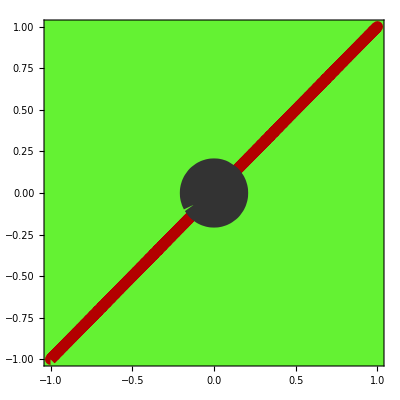

```mathematica
nr1= RegionPlot[y ≠ 0 && x/y ≠   1,{x,-1,1}, {y,-1,1}, PlotStyle -> trueStyle, BoundaryStyle -> trueStyle];
nr2= RegionPlot[y ≠ 0 && x/y ==  1,{x,-1,1}, {y,-1,1}, PlotStyle -> falseStyle, BoundaryStyle -> falseStyle];
nr3 = RegionPlot[x^2 + y^2 ≤ 0.02, {x,-1,1},{y,-1,1}, PlotStyle ->  undefStyle, BoundaryStyle -> undefStyle] ;
Show[nr1,nr2,nr3]
```

```mathematica
Show[r3]
```

```mathematica
Show[%647,Background->RGBColor[0.97,0.93,0.68]]
```